```mathematica
<<Matcher`;
```

```mathematica
?VF
```

VF[true_group, predicted_group] returns Error rate, FAR and FRR

```mathematica
(*use Distance_cls_cole.nb here*)
```

```mathematica
pg=classifyDist1[sdata,templ,1.3];
```

```mathematica
rr=Reap[For[i=0,i<4,i=i+0.05,
Sow[VF[tg,classifyDist1[sdata,templ,i]][[{2,3}]]];
]][[2,1]];
```

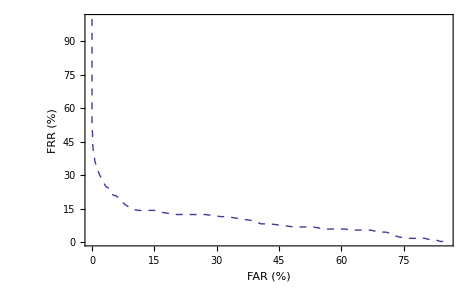

```mathematica
ListPlot[rr*100,Joined->True,Frame->True,FrameLabel->{"FAR (%)","FRR (%)"},AxesOrigin->{0,0},PlotStyle->Dashed]
```

```mathematica
(*EER*)
```

```mathematica
For[i=1,i<1.8,i=i+0.0005,
{far,frr}=VF[tg,classifyDist1[sdata,templ,i]][[{2,3}]];
If[Abs[far-frr]≤0.0001,Break[]];
];
{i,far,frr}
```

$Aborted

{1.3387,0.18175,0.12963}